```mathematica
a[n_]=2ArcTan[n^3];
seq=Table[N[a[n],10],{n,1,35}]
```

{1.570796327,2.89288266,3.067552422,3.110345196,3.12559299,3.13233346,3.135761766,3.13768641,3.138849171,3.13959265,3.140090024,3.140435246,3.140682321,3.140863791,3.141000061,3.141104372,3.14118557,3.141249718,3.14130107,3.141342654,3.141376694,3.141404825,3.141428275,3.141447978,3.14146465,3.141478862,3.141491043,3.14150155,3.14151065,3.14151858,3.141525519,3.14153162,3.141537001,3.14154177,3.141546006}

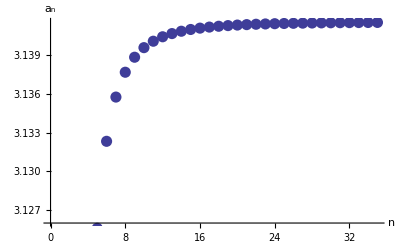

```mathematica
seqplot=ListPlot[seq,PlotStyle->PointSize[.02],AxesLabel->{"n","a_n"}]
```

```mathematica
f[x_,y_]=ⅇ^(-x^2-y^2);
surface=Plot3D[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->20]
```

-Graphics3D-